```mathematica
Mn = 0.9383;
Md = 1.8756;
conv = 0.197327;

MELEC = 0.000510999;
MMUON = 0.105658;
hbarc = 0.197327;
ALPHAEM = 1/137.036;
m=MELEC;
eta[Qsqr_]:= Qsqr / (2. * Md)^2

a1  = 1.57057 * conv^2;
a2  = 12.23792 * conv^2;
a3  = -42.04576 * conv^2;
a4  = 27.92014 * conv^2;
als1 = 1.52501 * conv^2;
als2 = 8.75139 * conv^2;
als3 = 15.97777 * conv^2;
als4 = 23.20415 * conv^2;
g0[Qsqr_]:= a1/(als1 + Qsqr) + a2/(als2 + Qsqr) + a3/(als3 + Qsqr) + a4/(als4 + Qsqr) 
b1  = 0.07043 * conv;
b2  = 0.14443 * conv;
b3  = -0.27343 * conv;
b4  = 0.05856 * conv;
bes1 = 43.67795 * conv^2;
bes2 = 30.05435 * conv^2;
bes3 = 16.43075 * conv^2;
bes4 = 2.80716 * conv^2;
g1[Qsqr_]:= Sqrt[Qsqr] * (b1/(bes1 + Qsqr) + b2/(bes2 + Qsqr) + b3/(bes3 + Qsqr) + b4/(bes4 + Qsqr)) 
c1  = -0.16577;
c2  = 0.27557;
c3  = -0.05382 ;
c4  = -0.05598;
gas1 = 1.87055 * conv^2;
gas2 = 14.95683 * conv^2;
gas3 = 28.04312 * conv^2;
gas4 = 41.12940 * conv^2;
g2[Qsqr_]:= Qsqr * (c1/(gas1 + Qsqr) + c2/(gas2 + Qsqr) + c3/(gas3 + Qsqr) + c4/(gas4 + Qsqr)) 

GC2[Qsqr_]:= 1 / (1 + Qsqr/4/0.807)^4/(2 eta[Qsqr] + 1) * ((1-2/3 eta[Qsqr]) g0[Qsqr] + 8/3 Sqrt[2 eta[Qsqr]] g1[Qsqr] + 2/3 (2 eta[Qsqr] - 1) g2[Qsqr])
GQ2[Qsqr_]:= 1 / (1 + Qsqr/4/0.807)^4/(2 eta[Qsqr] + 1) * (- g0[Qsqr] + Sqrt[2/eta[Qsqr]] g1[Qsqr] - (eta[Qsqr] + 1)/eta[Qsqr] g2[Qsqr])
GM2[Qsqr_]:= 1 / (1 + Qsqr/4/0.807)^4/(2 eta[Qsqr] + 1) * (2 g0[Qsqr] + 2(2 eta[Qsqr] - 1) / Sqrt[2 eta[Qsqr]] g1[Qsqr] -2 g2[Qsqr])
GC[Qsqr_]:= GC2[Qsqr]
GQ[Qsqr_]:= GQ2[Qsqr]
GM[Qsqr_]:= GM2[Qsqr]
```

```mathematica
τd =-t/(4*Md^2);
β=√(1-4*MELEC^2/Mll2);
r=√((s-Md^2-Mll2)^2-4 Md^2 Mll2);
a=β r Cos[θ];
b=β ((Mll2*(s-Md^2-Mll2)+t*(s-Md^2+Mll2))/r)Cos[θ]-β((2*(s-Md^2)√Mll2 ΔT)/r)Sin[θ]Cos[ϕ];
L=((Mll2-t)^2-b^2)/4;
s=Md^2+2Md Eγ;
A=(s-Md^2)^2 ΔT^2-t a (a+b)-Md^2 b^2-t(4 Md^2-t)Mll2 + MELEC^2/L(((Mll2-t)(a+b)-(s-Md^2)*b)^2+t(4 Md^2-t)(Mll2-t)^2);
B=(Mll2+t)^2+b^2+8*MELEC^2*Mll2-4*MELEC^2*(t+2*MELEC^2)/L*(Mll2-t)^2;
CE=A;
CM=A+(4 Md^2-t)B/2;
ΔT=1/(2 √s)√(1-((2s(t-2 Md^2)+(s+Md^2)(s+Md^2-Mll2))/(√((s-Md^2)^2((s-Md^2-Mll2)^2-4 Md^2 Mll2))))^2)r;
ds=ALPHAEM^3/(4π (s-Md^2)^2)β/(-t )^2 1/L(CE*(GC[-t]^2+8/9 GQ[-t]^2 τd^2)+CM*2/3 τd*GM[-t]^2)*(0.389379*10^6);
```

```mathematica
vals={t->-1,Eγ->8,Mll2->9};
```

```mathematica
CE1=t(s-Md^2)(s-Md^2-Mll2+t)(Mll2^2+6Mll2 t+t^2+4 m^2 Mll2)+(Mll2-t)^2(t^2 Mll2+Md^2(Mll2+t)^2+4 m^2 Md^2 Mll2);
CE2=-t(s-Md^2)(s-Md^2-Mll2+t)(Mll2^2+t^2+4 m^2(Mll2+2t-2 m^2))+(Mll2-t)^2(-Md^2(Mll2^2+t^2)+2 m^2(-t^2-2 Md^2 Mll2+4 m^2 Md^2));
CM1=CE1-2 Md^2(1+τd)(Mll2-t)^2(Mll2^2+t^2+4 m^2 Mll2);
CM2=CE2+2 Md^2(1+τd)(Mll2-t)^2(Mll2^2+t^2+4 m^2(Mll2-t-2 m^2));
vCE=CE1+CE2/β Log[(1+β)/(1-β)];
vCM=CM1+CM2/β Log[(1+β)/(1-β)];
dσdtdM2=(4 ALPHAEM^3 β)/((s-Md^2)^2 t^2(Mll2-t)^4)(vCE(GC[-t]^2+8/9 τd^2 GQ[-t]^2)+vCM 2/3 τd GM[-t]^2)*(0.389379*10^6);
```

```mathematica
data1=Table[{Cos[θ],NIntegrate[ds/.{t->-1.5,Eγ->8,Mll2->3.05^2},{ϕ,0,2π}]},{θ,0,Pi,0.05}];
data2=Table[{Cos[θ],NIntegrate[ds/.{t->-1.5,Eγ->7,Mll2->3.05^2},{ϕ,0,2π}]},{θ,0,Pi,0.05}];
data3=Table[{Cos[θ],NIntegrate[ds/.{t->-1.5,Eγ->6,Mll2->3.05^2},{ϕ,0,2π}]},{θ,0,Pi,0.05}];
```

```mathematica
data4=Table[{Cos[θ],NIntegrate[ds/.{t->-1.5,Eγ->8,Mll2->3.05^2},{ϕ,0,2π}]},{θ,0,Pi,0.05}];
data5=Table[{Cos[θ],NIntegrate[ds/.{t->-1,Eγ->8,Mll2->3.05^2},{ϕ,0,2π}]},{θ,0,Pi,0.05}];
data6=Table[{Cos[θ],NIntegrate[ds/.{t->-0.6,Eγ->8,Mll2->3.05^2},{ϕ,0,2π}]},{θ,0,Pi,0.05}];
```

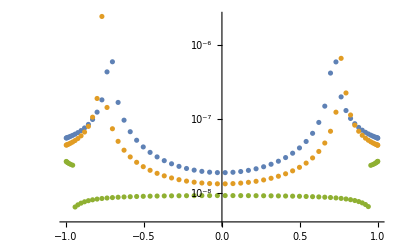

```mathematica
p1=ListLogPlot[{data1,data2,data3}];
Show[p1]
```

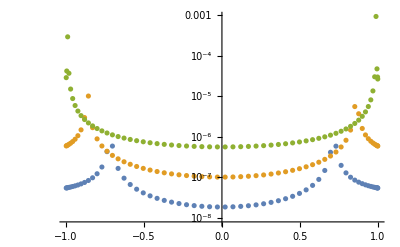

```mathematica
p2=ListLogPlot[{data4,data5,data6}];
Show[p2]
```

{-(6.77807×10^-12)/((100-(8.4591 Cos[θ]-5.33326 Cos[ϕ] Sin[θ])^2)^2),(3.17327×10^-13 Cos[θ]^2)/((100-(8.4591 Cos[θ]-5.33326 Cos[ϕ] Sin[θ])^2)^2),(8.30859×10^-12 Cos[θ] Cos[ϕ] Sin[θ])/((100-(8.4591 Cos[θ]-5.33326 Cos[ϕ] Sin[θ])^2)^2),(5.43859×10^-11 Cos[ϕ]^2 Sin[θ]^2)/((100-(8.4591 Cos[θ]-5.33326 Cos[ϕ] Sin[θ])^2)^2),(1.8215×10^-6)/(100-(8.4591 Cos[θ]-5.33326 Cos[ϕ] Sin[θ])^2),(1.04621×10^-6 Cos[θ]^2)/(100-(8.4591 Cos[θ]-5.33326 Cos[ϕ] Sin[θ])^2),(9.28082×10^-7 Cos[θ] Cos[ϕ] Sin[θ])/(100-(8.4591 Cos[θ]-5.33326 Cos[ϕ] Sin[θ])^2),-(4.28945×10^-7 Cos[ϕ]^2 Sin[θ]^2)/(100-(8.4591 Cos[θ]-5.33326 Cos[ϕ] Sin[θ])^2)}

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {3.1415}. NIntegrate obtained -2.78833×10^-6 and 1.62619×10^-10 for the integral and error estimates.

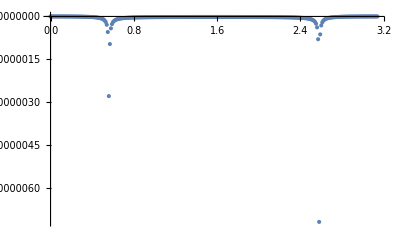

(9.28082×10^-7 Cos[θ] Cos[ϕ] Sin[θ])/(100-(8.4591 Cos[θ]-5.33326 Cos[ϕ] Sin[θ])^2)

{-(6.77807×10^-12)/((100-(8.4591 Cos[θ]-5.33326 Cos[ϕ] Sin[θ])^2)^2),(3.17327×10^-13 Cos[θ]^2)/((100-(8.4591 Cos[θ]-5.33326 Cos[ϕ] Sin[θ])^2)^2),(8.30859×10^-12 Cos[θ] Cos[ϕ] Sin[θ])/((100-(8.4591 Cos[θ]-5.33326 Cos[ϕ] Sin[θ])^2)^2),(5.43859×10^-11 Cos[ϕ]^2 Sin[θ]^2)/((100-(8.4591 Cos[θ]-5.33326 Cos[ϕ] Sin[θ])^2)^2),(1.8215×10^-6)/(100-(8.4591 Cos[θ]-5.33326 Cos[ϕ] Sin[θ])^2),(1.04621×10^-6 Cos[θ]^2)/(100-(8.4591 Cos[θ]-5.33326 Cos[ϕ] Sin[θ])^2),(9.28082×10^-7 Cos[θ] Cos[ϕ] Sin[θ])/(100-(8.4591 Cos[θ]-5.33326 Cos[ϕ] Sin[θ])^2),-(4.28945×10^-7 Cos[ϕ]^2 Sin[θ]^2)/(100-(8.4591 Cos[θ]-5.33326 Cos[ϕ] Sin[θ])^2)}

```mathematica
terms=Level[Expand[ds/.vals],1]
data2=Table[{θ,NIntegrate[terms[[8]],{ϕ,0,2Pi}]},{θ,0,Pi,0.01}];
ListPlot[data2,PlotRange->Full]
terms[[7]]
terms
```

```mathematica
(** Looking for term which dominates the ϕ integration **)
(** This term has a denominator = (Mll2-t)^2-(b1 Cos[θ] + b2 Sin[θ] Cos[ϕ])^2
```

```mathematica
NIntegrate[Sin[θ](terms[[6]]+terms[[5]]+terms[[7]]+terms[[8]]),{ϕ,0,2Pi},{θ,0,Pi}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

2.21264×10^-6

```mathematica
dσdtdM2/.vals
```

2.24063×10^-6

```mathematica
B2/.vals
```

-5.33326

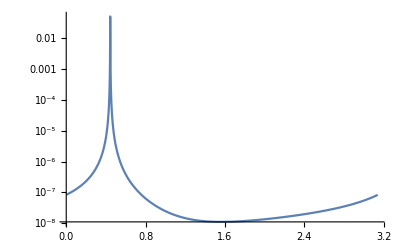

```mathematica
LogPlot[ds/.{t->-1,Eγ->8,Mll2->10,ϕ->π},{θ,0,π},PlotRange->Full]
```

```mathematica
ds/.{t->-1,Eγ->8,Mll2->10,ϕ->π,θ->0.5}
```

3.24103×10^-6

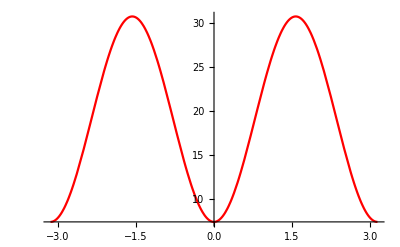

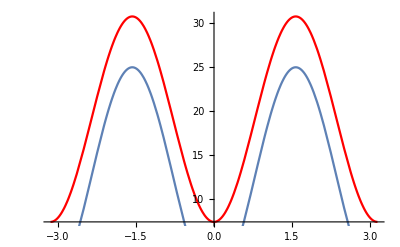

```mathematica
mll2=10;
eγ=8;
T=-1.1;
p1=Plot[L/.{Eγ->eγ,Mll2->mll2,t->T,ϕ->π/2},{θ,-π,π},PlotStyle->Red]
p2=Plot[mll2^2 Sin[θ]^2/4,{θ,-Pi,Pi}];
Show[p1,p2]
```

```mathematica
L/.{Eγ->8,Mll2->10,t->-1.5,ϕ->0.5}
```

1/4 (132.25-(8.69303 Cos[θ]-6.60705 Sin[θ])^2)

```mathematica
b/.{t->0,Mll2->100}
```

(100. (-100.+3.7512 Eγ) Cos[θ])/(√(-1407.15+(-100.+3.7512 Eγ)^2))-(10. (0.+3.7512 Eγ) √(1-(-14.0715 (3.51788+3.7512 Eγ)+(-92.9642+3.7512 Eγ) (7.03575+3.7512 Eγ))^2/((0.+3.7512 Eγ)^2 (-1407.15+(-100.+3.7512 Eγ)^2))) Cos[ϕ] Sin[θ])/(√(3.51788+3.7512 Eγ))

Calculating I_A

```mathematica
1/(2π)Integrate[IA,{θ,0,Pi},{ϕ,0.0,2Pi}]
8/(Mll2-t)^4(t(s-Md^2)(s-Md^2-Mll2+t)(Mll2^2+6Mll2 t + t^2+4 m^2 Mll2)+(Mll2-t)^2(t^2 Mll2+Md^2(Mll2+t)^2+4 m^2 Md^2 Mll2)+1/β Log[(1+β)/(1-β)](-t(s-Md^2)(s-Md^2-Mll2+t)(Mll2^2+t^2+4 m^2(Mll2+2t-2 m^2))+(Mll2-t)^2(-Md^2(Mll2^2+t^2)+2 m^2(-t^2-2 Md^2 Mll2+4 m^2 Md^2))))/.vals
```

3.14159 IA

241.296

```mathematica
IA=Expand[FullSimplify[Sin[θ] A/L/.vals]]
```

(205.073 Sin[θ])/((3.8976-2.8976 Cos[θ]^2+3.40447 Cos[θ] Cos[ϕ] Sin[θ]-1. Cos[ϕ]^2 Sin[θ]^2)^2)-(53.0691 Cos[θ]^2 Sin[θ])/((3.8976-2.8976 Cos[θ]^2+3.40447 Cos[θ] Cos[ϕ] Sin[θ]-1. Cos[ϕ]^2 Sin[θ]^2)^2)-(73.8888 Cos[θ]^4 Sin[θ])/((3.8976-2.8976 Cos[θ]^2+3.40447 Cos[θ] Cos[ϕ] Sin[θ]-1. Cos[ϕ]^2 Sin[θ]^2)^2)+(314.282 Cos[θ] Cos[ϕ] Sin[θ]^2)/((3.8976-2.8976 Cos[θ]^2+3.40447 Cos[θ] Cos[ϕ] Sin[θ]-1. Cos[ϕ]^2 Sin[θ]^2)^2)-(13.6648 Cos[θ]^3 Cos[ϕ] Sin[θ]^2)/((3.8976-2.8976 Cos[θ]^2+3.40447 Cos[θ] Cos[ϕ] Sin[θ]-1. Cos[ϕ]^2 Sin[θ]^2)^2)-(107.46 Cos[ϕ]^2 Sin[θ]^3)/((3.8976-2.8976 Cos[θ]^2+3.40447 Cos[θ] Cos[ϕ] Sin[θ]-1. Cos[ϕ]^2 Sin[θ]^2)^2)+(133.329 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^3)/((3.8976-2.8976 Cos[θ]^2+3.40447 Cos[θ] Cos[ϕ] Sin[θ]-1. Cos[ϕ]^2 Sin[θ]^2)^2)-(82.5825 Cos[θ] Cos[ϕ]^3 Sin[θ]^4)/((3.8976-2.8976 Cos[θ]^2+3.40447 Cos[θ] Cos[ϕ] Sin[θ]-1. Cos[ϕ]^2 Sin[θ]^2)^2)+(14.0715 Cos[ϕ]^4 Sin[θ]^5)/((3.8976-2.8976 Cos[θ]^2+3.40447 Cos[θ] Cos[ϕ] Sin[θ]-1. Cos[ϕ]^2 Sin[θ]^2)^2)

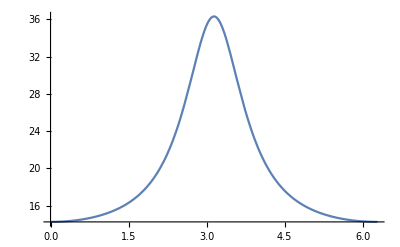

```mathematica
Plot[IA/.{θ->1},{ϕ,0,2Pi}]
```

```mathematica
Integrate[IA,{ϕ,0,Pi}]
```

$Aborted